## Figure 2A, 2B

Evaluate notebook to generate plots for Fig. 2A (an example of well-mixed dynamics, for two initial conditions),  and 2B (an example of spatial dynamics, for two initial conditions).

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Statics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)
steps=10000;
```

### Numeric parameters

```mathematica
d=1; //N(*diffusion coefficient*)
l=10//N;
s1=0.4;
s2=supply-s1;
s={s1,s2};
SeedRandom[56];
alphas=Table[RandomReal[{.1(i-1),.1i}],{i,10}];
alphas=RandomSample[alphas];

α=Table[{alphas[[i]],e-alphas[[i]]},{i,Length[alphas]}];
```

```mathematica
m=Length[α];
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

```mathematica
colors=ParulaCM/@alphas
```

{RGBColor[0.07844918784897215, 0.5235971372887688, 0.8301795658963089],RGBColor[0.9442280385120374, 0.7261065637969653, 0.28905726593379927],RGBColor[0.36799317980686796, 0.7438929047104224, 0.5376571533397793],RGBColor[0.03883151875508706, 0.37167775674221026, 0.8741638383978186],RGBColor[0.022778128314106857, 0.6535041569645974, 0.7767295240050872],RGBColor[0.7560093678283482, 0.7381007032365035, 0.37538369746016037],RGBColor[0.06517846318782149, 0.6859813594516865, 0.7206758832039522],RGBColor[0.14126135222219546, 0.31287939156748945, 0.8123233841747916],RGBColor[0.5265905388870171, 0.7491100883282099, 0.4675455909147763],RGBColor[0.9743760089684801, 0.9771286216643976, 0.05789948415237574]}

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

### Strategy plotting

```mathematica
colors=Table[ColorData[97,i],{i,m}];
p=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

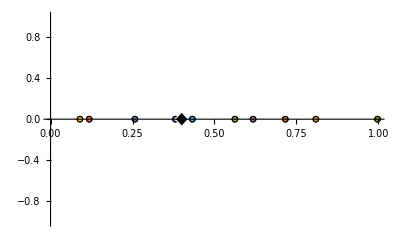

```mathematica
Show[ListPlot[Table[{{strat[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->{0,.2,.4,.6,.8,1},PlotMarkers->p,TicksStyle->Directive[Black,12]],Graphics[{EdgeForm[{White}],Polygon[{{.4-.02,0},{.4,.07},{.4+.02,0},{.4,-.07}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["fig2A_inset_strategies.svg",%,"SVG"];
```

### show unique fp for spatial model using different IC

```mathematica
perturbSteps=7000;
```

```mathematica
nInit1=l*ConstantArray[1/m,m]//N;
```

```mathematica
y=(1-.9-.0002)/7;
nInit2=l*{y,y,y,.0001,y,y,.9,.0001,y,y};
```

```mathematica
solIC1=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit1},n,{t,0,perturbSteps}];
solIC2=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit2},n,{t,0,perturbSteps}];
```

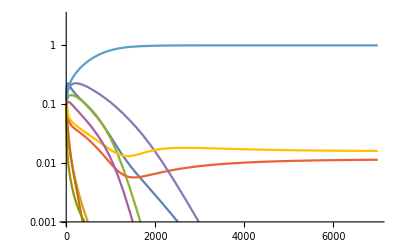

```mathematica
logSeriesPlotIC1=LogPlot[Evaluate[Table[Indexed[solIC1[t],i]/l,{i,m}]],{t,0,perturbSteps},PlotRange->{{0,perturbSteps},{10^-3,3}},Ticks->{Range[0,7000,1000],{.001,.01,.1,1}},TicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig2B_top_timeseries.svg",%,"SVG"];
```

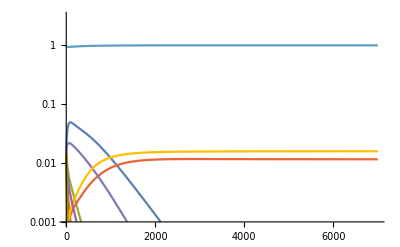

```mathematica
logSeriesPlotIc2=LogPlot[Evaluate[Table[Indexed[solIC2[t],i]/l,{i,m}]],{t,0,perturbSteps},PlotRange->{{0,perturbSteps},{10^-3,3}},Ticks->{Range[0,7000,1000],{.001,.01,.1,1}},TicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig2B_bottom_timeseries.svg",%,"SVG"];
```

### Well mixed comparison

```mathematica
s1=l*s1;
s2=l*s2;
```

```mathematica
growthRate[pops_,thisSpecies_]:=
Module[{thisDiversity,thisStrat,interactionNutrient1,interactionNutrient2,growth,thisSpeciesPosition},
thisDiversity=Length[pops];
thisStrat=α[[thisSpecies]];

interactionNutrient1=Sum[pops[[i]]*α[[i,1]],{i,thisDiversity}];
interactionNutrient2=Sum[pops[[i]]*α[[i,2]],{i,thisDiversity}];

growth=(thisStrat[[1]]*s1/interactionNutrient1+thisStrat[[2]]*s2/interactionNutrient2)*pops[[thisSpecies]]
];
```

```mathematica
evolveN[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,positions,n0,nNew},
n0=n;
growthTable=Table[growthRate[n0,i],{i,Length[n0]}];
dn=growthTable-δ*n0
];
```

```mathematica
wmStep=100;
```

```mathematica
wellMixedInit1=nInit1;
wellMixedInit2={.05,.05,.05,.05,.2,.2,.1,.1,.1,.1}*l;
```

```mathematica
wellMixedSol1=NDSolveValue[{n'[t]==evolveN[n[t]],n[0]==wellMixedInit1},n,{t,0,wmStep}];
wellMixedSol2=NDSolveValue[{n'[t]==evolveN[n[t]],n[0]==wellMixedInit2},n,{t,0,wmStep}];
```

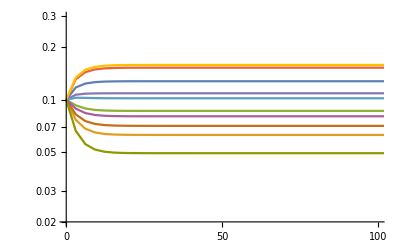

```mathematica
wellMixedLogSeriesPlot=LogPlot[Evaluate[Table[Indexed[wellMixedSol1[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{{0,wmStep},{2*10^-2,.3}},Ticks->{Range[0,100,50],{.025,.05,.1,.2}},TicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig2A_top_timeseries.svg",%,"SVG"];
```

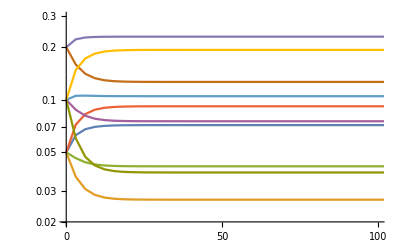

```mathematica
wellMixedLogSeriesPlot1=LogPlot[Evaluate[Table[Indexed[wellMixedSol2[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{{0,wmStep},{2*10^-2,.3}},Ticks->{Range[0,100,50],{.025,.05,.1,.2}},TicksStyle->Black,LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig2A_bottom_timeseries.svg",%,"SVG"];
```